# SVM-BDT Comparison Results

## Raw Data

## SVM: c, γ, Number of Support Vectors, False Positive Fraction, False Negative Fraction, Efficiency

```mathematica
SVMLinearRawData= Import ["~/Desktop/ATLAS/libsvm/testdata/results/results-linear", "Table"];
SVMCircleRawData= Import ["~/Desktop/ATLAS/libsvm/testdata/results/results-circle", "Table"];
SVMTwoCircleRawData = Import ["~/Desktop/ATLAS/libsvm/testdata/results/results-twocircle", "Table"];
SVMTwoSphereRawData = Import ["~/Desktop/ATLAS/libsvm/testdata/results/results-twosphere", "Table"];
SVMTwoSphere100kRawData= Import ["~/Desktop/ATLAS/libsvm/testdata/results/results-twosphere100k", "Table"];
```

## BDT: Stumps, Efficiency, False Positive Fraction, False Negative Fraction

```mathematica
BDTLinearRawData = Import ["~/Desktop/ATLAS/WEKA/results/results-linear", "Table"];
BDTCircleRawData = Import ["~/Desktop/ATLAS/WEKA/results/results-circle", "Table"];
BDTTwoCircleRawData = Import ["~/Desktop/ATLAS/WEKA/results/results-twocircle", "Table"];
BDTTwoSphereRawData = Import ["~/Desktop/ATLAS/WEKA/results/results-twosphere", "Table"];
```

## Formatted Datasets

## SVM

### c-γ-Efficiency

```mathematica
SVMLinearCGE = SVMLinearRawData[[All,{1,2, 6}]];
SVMCircleCGE = SVMCircleRawData[[All,{1,2, 6}]];
SVMTwoCircleCGE = SVMTwoCircleRawData[[All,{1,2, 6}]];
SVMTwoSphereCGE = SVMTwoSphereRawData[[All,{1,2, 6}]];
SVMTwoSphere100kCGE = SVMTwoSphere100kRawData[[All,{1,2, 6}]];
```

### Log(c)-γ-Efficiency

```mathematica
SVMLinearLogCGE = MapAt[Log10, SVMLinearCGE, {All, 1}];
SVMCircleLogCGE = MapAt[Log10, SVMCircleCGE, {All, 1}];
SVMTwoCircleLogCGE = MapAt[Log10, SVMTwoCircleCGE, {All, 1}];
SVMTwoSphereLogCGE = MapAt[Log10, SVMTwoSphereCGE, {All, 1}];
SVMTwoSphere100kLogCGE = MapAt[Log10, SVMTwoSphere100kCGE, {All, 1}];
```

### Efficiency-1 - False Positive Fraction

```mathematica
SVMLinearEFP= MapAt[1-#&,SVMLinearRawData[[All,{6,4}]],{All,2}];
SVMCircleEFP = MapAt[1-#&,SVMCircleRawData[[All,{6,4}]],{All,2}];
SVMTwoCircleEFP = MapAt[1-#&,SVMTwoCircleRawData[[All,{6,4}]],{All,2}];
SVMTwoSphereEFP = MapAt[1-#&,SVMTwoSphereRawData[[All,{6,4}]],{All,2}];
SVMTwoSphere100kEFP= MapAt[1-#&,SVMTwoSphere100kRawData[[All,{6,4}]],{All,2}];
```

### Efficiency-1 - False Negative Fraction

```mathematica
SVMLinearEFN= MapAt[1-#&,SVMLinearRawData[[All,{6,5}]],{All,2}];
SVMCircleEFN = MapAt[1-#&,SVMCircleRawData[[All,{6,5}]],{All,2}];
SVMTwoCircleEFN = MapAt[1-#&,SVMTwoCircleRawData[[All,{6,5}]],{All,2}];
SVMTwoSphereEFN = MapAt[1-#&,SVMTwoSphereRawData[[All,{6,5}]],{All,2}];
SVMTwoSphere100kEFN = MapAt[1-#&,SVMTwoSphere100kRawData[[All,{6,5}]],{All,2}];
```

### False Positive Fraction-1 - False Negative Fraction

```mathematica
SVMLinearFPFN= MapAt[1-#&,SVMLinearRawData[[All,{4,5}]],{All,2}];
SVMCircleFPFN = MapAt[1-#&,SVMCircleRawData[[All,{4,5}]],{All,2}];
SVMTwoCircleFPFN = MapAt[1-#&,SVMTwoCircleRawData[[All,{4,5}]],{All,2}];
SVMTwoSphereFPFN = MapAt[1-#&,SVMTwoSphereRawData[[All,{4,5}]],{All,2}];
SVMTwoSphere100kFPFN = MapAt[1-#&,SVMTwoSphere100kRawData[[All,{4,5}]],{All,2}];
```

## BDT

### Stumps-Efficiency

```mathematica
BDTLinearSE = BDTLinearRawData[[All,{1,2}]];
BDTCircleSE = BDTCircleRawData[[All,{1,2}]];
BDTTwoCircleSE = BDTTwoCircleRawData[[All,{1,2}]];
BDTTwoSphereSE = BDTTwoSphereRawData[[All,{1,2}]];
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDTLinearEFP = MapAt[1-#&,BDTLinearRawData[[All,{2,3}]],{All,2}];
BDTCircleEFP = MapAt[1-#&,BDTCircleRawData[[All,{2,3}]],{All,2}];
BDTTwoCircleEFP = MapAt[1-#&,BDTTwoCircleRawData[[All,{2,3}]],{All,2}];
BDTTwoSphereEFP = MapAt[1-#&,BDTTwoSphereRawData[[All,{2,3}]],{All,2}];
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDTLinearEFN = MapAt[1-#&,BDTLinearRawData[[All,{2,4}]],{All,2}];
BDTCircleEFN = MapAt[1-#&,BDTCircleRawData[[All,{2,4}]],{All,2}];
BDTTwoCircleEFN = MapAt[1-#&,BDTTwoCircleRawData[[All,{2,4}]],{All,2}];
BDTTwoSphereEFN = MapAt[1-#&,BDTTwoSphereRawData[[All,{2,4}]],{All,2}];
```

### False Positive Fraction-1 - False Negative Fraction

```mathematica
BDTLinearFPFN= MapAt[1-#&,BDTLinearRawData[[All,{3,4}]],{All,2}];
BDTCircleFPFN = MapAt[1-#&,BDTCircleRawData[[All,{3,4}]],{All,2}];
BDTTwoCircleFPFN = MapAt[1-#&,BDTTwoCircleRawData[[All,{3,4}]],{All,2}];
BDTTwoSphereFPFN = MapAt[1-#&,BDTTwoSphereRawData[[All,{3,4}]],{All,2}];
```

## Optimizing Parameters

## SVM

```mathematica
SVMLinearBest = Last[SortBy[SVMLinearCGE,Last]];
SVMCircleBest = Last[SortBy[SVMCircleCGE,Last]];
SVMTwoCircleBest =Last[SortBy[SVMTwoCircleCGE,Last]];
SVMTwoSphereBest =Last[SortBy[SVMTwoSphereCGE,Last]];
SVMTwoSphere100kBest =Last[SortBy[SVMTwoSphere100kCGE,Last]];

SVMBestResultTable = Grid[{{"Data Set","c","γ","Efficiency"},Prepend[SVMLinearBest,"Linear"],Prepend[SVMCircleBest,"Circle"],Prepend[SVMTwoCircleBest,"Two Circle"],Prepend[SVMTwoSphereBest,"Two Sphere"],Prepend[SVMTwoSphere100kBest, "Two Sphere 100K"]},Frame->All];
```

## BDT

```mathematica
BDTLinearBest = Last[SortBy[BDTLinearSE,Last]];
BDTCircleBest = Last[SortBy[BDTCircleSE,Last]];
BDTTwoCircleBest =Last[SortBy[BDTTwoCircleSE,Last]];
BDTTwoSphereBest =Last[SortBy[BDTTwoSphereSE,Last]];

BDTBestResultTable = Grid[{{"Data Set","Stumps","Efficiency"},Prepend[BDTLinearBest,"Linear"],Prepend[BDTCircleBest,"Circle"],Prepend[BDTTwoCircleBest,"Two Circle"],Prepend[BDTTwoSphereBest,"Two Sphere"]},Frame->All];
```

## Developing Plots

## SVM

### c-γ-Efficiency

```mathematica
SVMLinearCGEPlot=ListPlot3D[SVMLinearCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Linear c-γ-Efficiency",PlotStyle->Green];
SVMCircleCGEPlot = ListPlot3D[SVMCircleCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Circle c-γ-Efficiency",PlotStyle->Green];
SVMTwoCircleCGEPlot = ListPlot3D[SVMTwoCircleCGE, AxesLabel->{c, γ, Efficiency},PlotLabel->"SVM Two Circle c-γ-Efficiency",PlotStyle->Green];
SVMTwoSphereCGEPlot = ListPlot3D[SVMTwoSphereCGE, AxesLabel->{c, γ, Efficiency},PlotLabel->"SVM Two Sphere c-γ-Efficiency",PlotStyle->Green];
SVMTwoSphere100kCGEPlot = ListPlot3D[SVMTwoSphere100kCGE, AxesLabel->{c, γ, Efficiency},PlotLabel->"SVM Two Sphere c-γ-Efficiency (100K Events)",PlotStyle->Green];
```

### Log(c)-γ-Efficiency

```mathematica
SVMLinearLogCGEPlot=ListPlot3D[SVMLinearLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Linear Log c-γ-Efficiency",PlotStyle->Green];
SVMCircleLogCGEPlot=ListPlot3D[SVMCircleLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Circle Log c-γ-Efficiency",PlotStyle->Green];
SVMTwoCircleLogCGEPlot = ListPlot3D[SVMTwoCircleLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Two Circle Log c-γ-Efficiency",PlotStyle->Green];
SVMTwoSphereLogCGEPlot = ListPlot3D[SVMTwoSphereLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Two Sphere Log c-γ-Efficiency",PlotStyle->Green];
SVMTwoSphere100kLogCGEPlot = ListPlot3D[SVMTwoSphere100kLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Two Sphere Log c-γ-Efficiency (100K Events)",PlotStyle->Green];
```

### Efficiency-(1- False Positive Fraction)

```mathematica
SVMLinearEFPPlot = ListPlot[SVMLinearEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Linear Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMCircleEFPPlot = ListPlot[SVMCircleEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Circle Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleEFPPlot = ListPlot[SVMTwoCircleEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Two Circle Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMTwoSphereEFPPlot = ListPlot[SVMTwoSphereEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Two Sphere Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMTwoSphere100kEFPPlot = ListPlot[SVMTwoSphere100kEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Two Sphere Efficiency-False Positive Fraction (100K Events)",PlotStyle->Darker[Green]];
```

### Efficiency-(1-False Negative Fraction)

```mathematica
SVMLinearEFNPlot = ListPlot[SVMLinearEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Linear Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMCircleEFNPlot = ListPlot[SVMCircleEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Circle Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleEFNPlot = ListPlot[SVMTwoCircleEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoSphereEFNPlot = ListPlot[SVMTwoSphereEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Two Sphere Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoSphere100kEFNPlot = ListPlot[SVMTwoSphere100kEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Two Sphere Efficiency-1 - False Negative Fraction (100K Events)",PlotStyle->Darker[Green]];
```

### False Positive Fraction-(1-False Negative Fraction)

```mathematica
SVMLinearFPFNPlot = ListPlot[SVMLinearFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Linear False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMCircleFPFNPlot = ListPlot[SVMCircleFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Circle False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleFPFNPlot = ListPlot[SVMTwoCircleFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoSphereFPFNPlot = ListPlot[SVMTwoSphereFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Two Sphere False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoSphere100kFPFNPlot = ListPlot[SVMTwoSphere100kFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Two Sphere False Positive Fraction-1 - False Negative Fraction (100K Events)",PlotStyle->Darker[Green]];
```

## BDT

### Stumps-Efficiency

```mathematica
BDTLinearSEPlot = ListPlot[BDTLinearSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Linear Stumps-Efficiency",PlotStyle->Red];
BDTCircleSEPlot = ListPlot[BDTCircleSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Circle Stumps-Efficiency",PlotStyle->Red];
BDTTwoCircleSEPlot = ListPlot[BDTTwoCircleSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Two Circle Stumps-Efficiency",PlotStyle->Red];
BDTTwoSphereSEPlot = ListPlot[BDTTwoSphereSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Two Sphere Stumps-Efficiency",PlotStyle->Red];
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDTLinearEFPPlot = ListPlot[BDTLinearEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Linear Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDTCircleEFPPlot = ListPlot[BDTCircleEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Circle Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDTTwoCircleEFPPlot = ListPlot[BDTTwoCircleEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Two Circle Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDTTwoSphereEFPPlot = ListPlot[BDTTwoSphereEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Two Sphere Efficiency-1 - False Positive Fraction",PlotStyle->Red];
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDTLinearEFNPlot = ListPlot[BDTLinearEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Linear Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDTCircleEFNPlot = ListPlot[BDTCircleEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Circle Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDTTwoCircleEFNPlot = ListPlot[BDTTwoCircleEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDTTwoSphereEFNPlot = ListPlot[BDTTwoSphereEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Two Sphere Efficiency-1 - False Negative Fraction",PlotStyle->Red];
```

### False Positive Fraction-(1-False Negative Fraction)

```mathematica
BDTLinearFPFNPlot = ListPlot[BDTLinearFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Linear False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDTCircleFPFNPlot = ListPlot[BDTCircleFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Circle False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDTTwoCircleFPFNPlot = ListPlot[BDTTwoCircleFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDTTwoSphereFPFNPlot = ListPlot[BDTTwoSphereFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Two Sphere False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
```

## Visualizing Results

## Optimized Parameters

### SVM

```mathematica
SVMBestResultTable
```

Data Set | c | γ | Efficiency
Linear | 0.562341 | 6. | 0.965657
Circle | 10. | 1. | 0.935484
Two Circle | 100. | 1. | 0.857143
Two Sphere | 17.7828 | 1. | 0.793522
Two Sphere 100K | 100. | 1. | 0.815769

### BDT

```mathematica
BDTBestResultTable
```

Data Set | Stumps | Efficiency
Linear | 60 | 0.955
Circle | 100 | 0.979
Two Circle | 180 | 0.852
Two Sphere | 1000 | 0.9488

## Plots

### SVM

#### c-γ-Efficiency

```mathematica
SVMLinearCGEPlot
SVMCircleCGEPlot
SVMTwoCircleCGEPlot
SVMTwoSphereCGEPlot
SVMTwoSphere100kCGEPlot
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

#### Log(c)-γ-Efficiency

```mathematica
SVMLinearLogCGEPlot
SVMCircleLogCGEPlot
SVMTwoCircleLogCGEPlot
SVMTwoSphereLogCGEPlot
SVMTwoSphere100kLogCGEPlot
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

#### Efficiency-(1- False Positive Fraction)

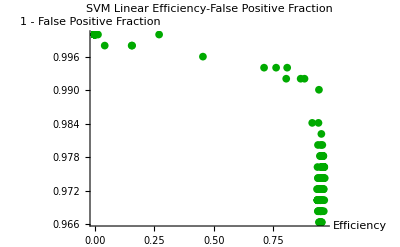

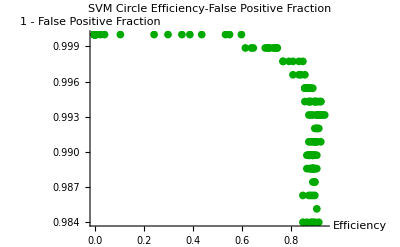

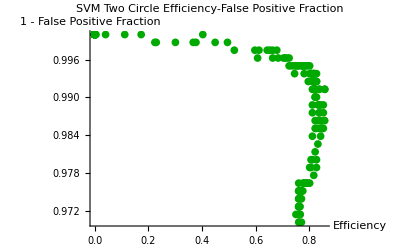

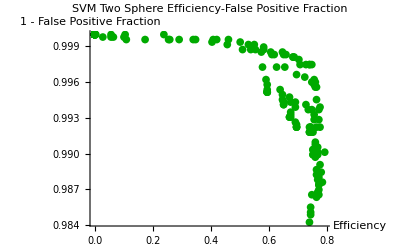

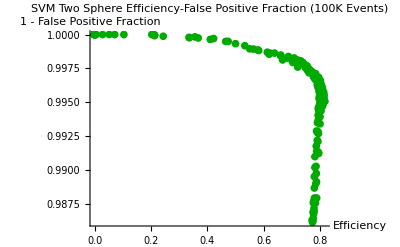

```mathematica
SVMLinearEFPPlot
SVMCircleEFPPlot
SVMTwoCircleEFPPlot
SVMTwoSphereEFPPlot
SVMTwoSphere100kEFPPlot
```

#### Efficiency-(1-False Negative Fraction)

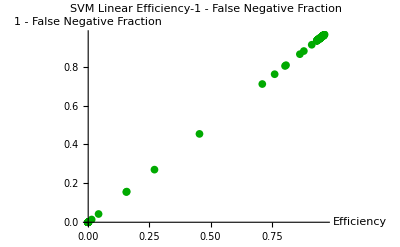

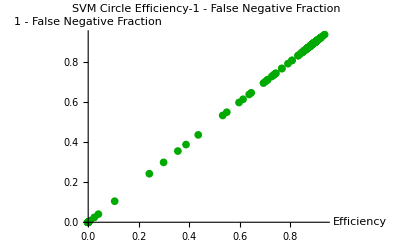

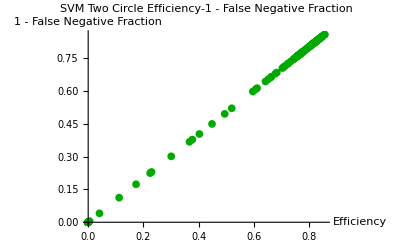

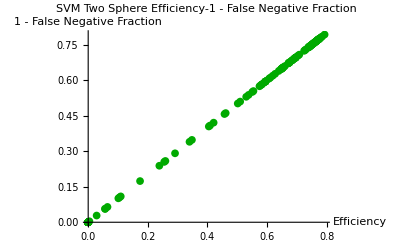

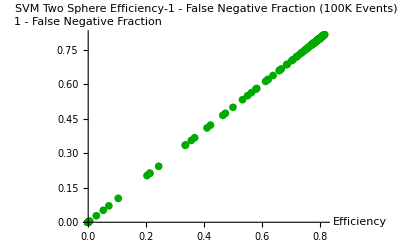

```mathematica
SVMLinearEFNPlot
SVMCircleEFNPlot
SVMTwoCircleEFNPlot
SVMTwoSphereEFNPlot
SVMTwoSphere100kEFNPlot
```

#### False Positive Fraction-(1-False Negative Fraction)

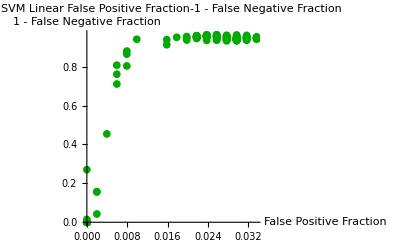

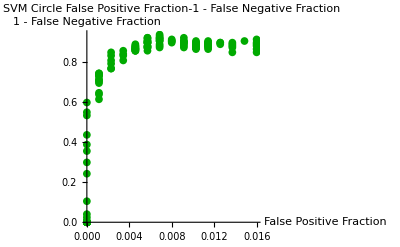

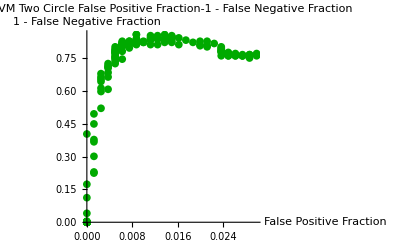

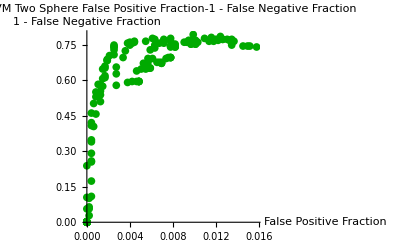

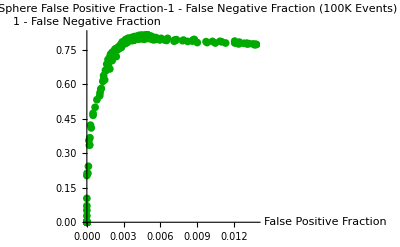

```mathematica
SVMLinearFPFNPlot
SVMCircleFPFNPlot
SVMTwoCircleFPFNPlot
SVMTwoSphereFPFNPlot
SVMTwoSphere100kFPFNPlot
```

### BDT

#### Folds-Stumps-Efficiency

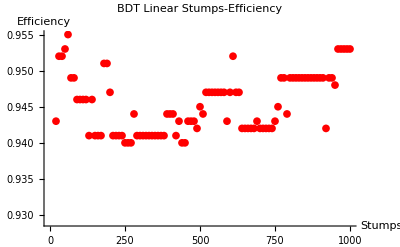

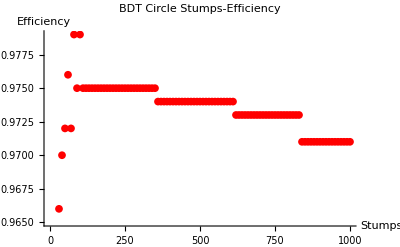

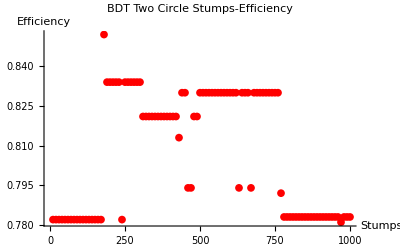

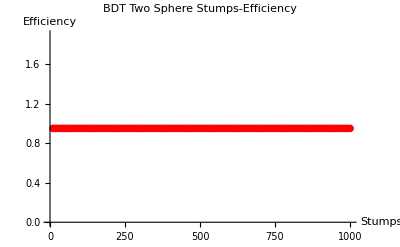

```mathematica
BDTLinearSEPlot
BDTCircleSEPlot
BDTTwoCircleSEPlot
BDTTwoSphereSEPlot
```

#### Efficiency-1 - False Positive Fraction

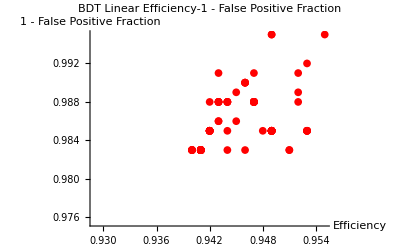

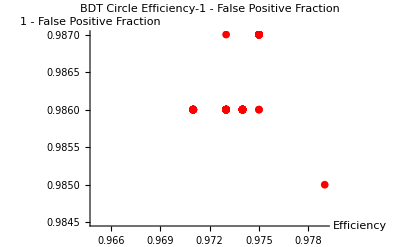

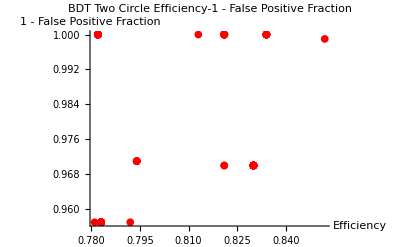

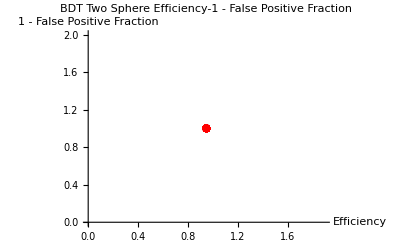

```mathematica
BDTLinearEFPPlot
BDTCircleEFPPlot
BDTTwoCircleEFPPlot
BDTTwoSphereEFPPlot
```

#### Efficiency-1 - False Negative Fraction

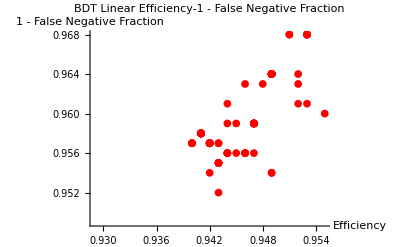

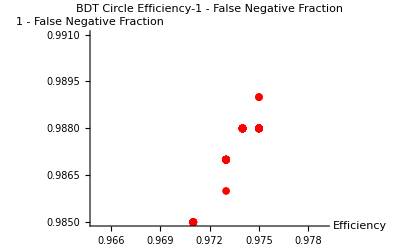

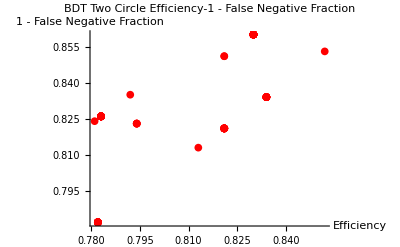

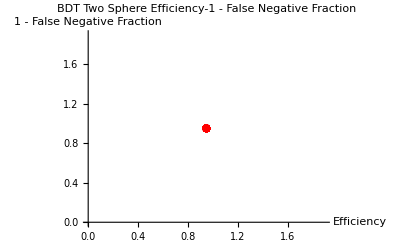

```mathematica
BDTLinearEFNPlot
BDTCircleEFNPlot
BDTTwoCircleEFNPlot
BDTTwoSphereEFNPlot
```

#### False Positive Fraction-1 - False Negative Fraction

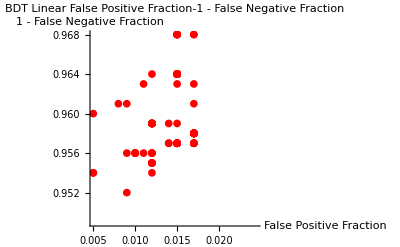

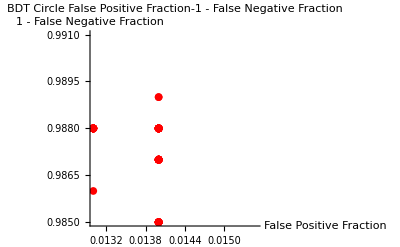

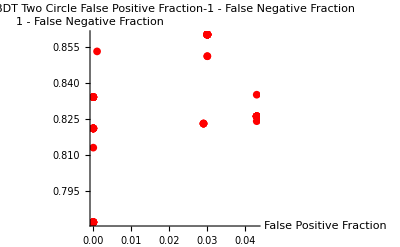

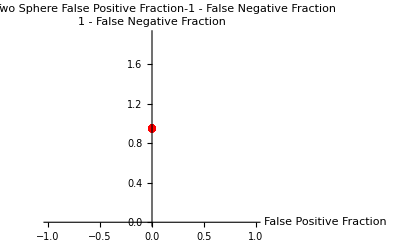

```mathematica
BDTLinearFPFNPlot
BDTCircleFPFNPlot
BDTTwoCircleFPFNPlot
BDTTwoSphereFPFNPlot
```

### Merged

#### False Positive Fraction- 1 - False Negative Fraction

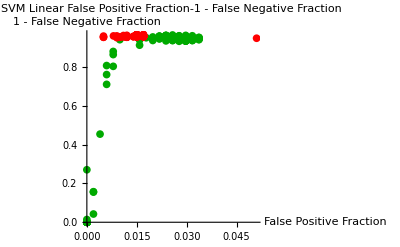

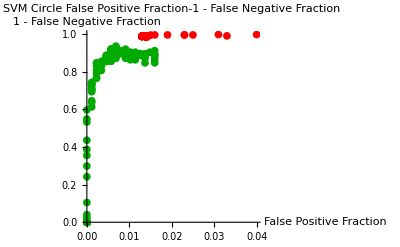

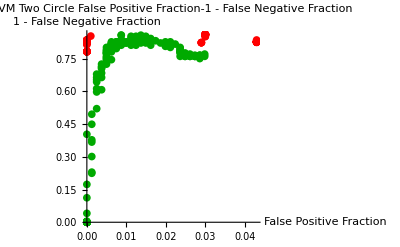

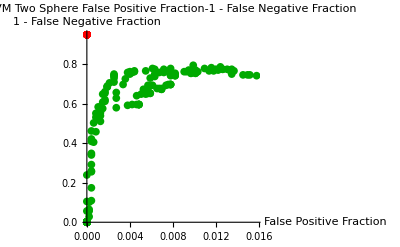

```mathematica
Show[SVMLinearFPFNPlot,BDTLinearFPFNPlot,PlotRange-> All]
Show[SVMCircleFPFNPlot,BDTCircleFPFNPlot,PlotRange-> All]
Show[SVMTwoCircleFPFNPlot,BDTTwoCircleFPFNPlot,PlotRange-> All]
Show[SVMTwoSphereFPFNPlot,BDTTwoSphereFPFNPlot,PlotRange-> All]
```